```mathematica
w=((1+α) (c+2 c α+a (α+θ))-(1+2 α) (1+α-μ α) Subscript[c, r])/(2 (1+α) (1+2 α))
```

6.1127

```mathematica
pm=(2 (1+α)^2 (c+2 c α+a (1+α-θ)) (-2+Subscript[τ, r])+2 (1+α)^2 (1+2 α) Subscript[c, d] (-2+Subscript[τ, r])+Subscript[τ, m] ((1+α) (c α (1+2 α)+a (4+α (8+α)))-a (4+3 α (3+α)) θ+α (1+2 α) (1+α-α μ) Subscript[c, r]-2 a (1+2 α) (1+α-θ) Subscript[τ, r]))/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

(0.277778 (0.9 (112.058-57.6 τ_r)+80.36 (-2+τ_r)))/(0.9 (3.76-1.8 τ_r)+3.92 (-2+τ_r))

```mathematica
pr=(-2 (1+α) (2 a α (1+α)+c (1+2 α)^2+a (3+4 α) θ)-(1+α) (1+2 α) (-1+α (-1+μ)) Subscript[c, r] (-2+Subscript[τ, m])+(c (1+α)^2 (1+2 α)+a (3+α (6+α)) (α+θ)) Subscript[τ, m]+2 α (1+α) (1+2 α) Subscript[c, d] (-1+Subscript[τ, r])+2 ((1+α) (α (a+c+a α+2 c α)+a (2+3 α) θ)-a (1+2 α) (α+θ) Subscript[τ, m]) Subscript[τ, r])/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

(0.277778 (-132.542+1.008 (-1+τ_r)+78.112 τ_r))/(0.9 (3.76-1.8 τ_r)+3.92 (-2+τ_r))

```mathematica
a=20
c=2
Subscript[c, r]=1
Subscript[c, d] =0.5
θ=0.6
α=0.4
μ=0.3
```

20

2

1

0.5

0.6

0.4

0.3

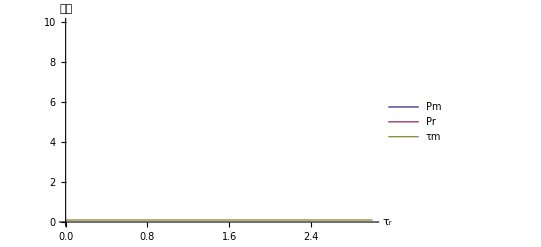

```mathematica
p1=Plot[{pm,pr,Subscript[τ, m]=0.1},{Subscript[τ, r],0,3},AxesLabel->{Subscript[τ, r],价格},PlotLegends->Placed[{Pm,Pr,τm},Center],PlotRange->{0,10}]
```

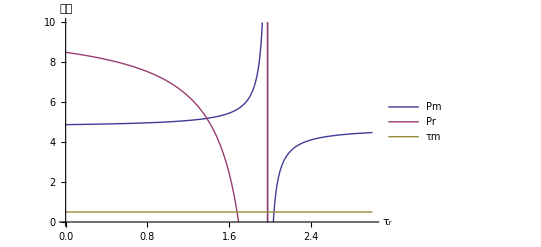

```mathematica
p1=Plot[{pm,pr,Subscript[τ, m]=0.5},{Subscript[τ, r],0,3},AxesLabel->{Subscript[τ, r],价格},PlotLegends->Placed[{Pm,Pr,τm},Center],PlotRange->{0,10}]
```

```mathematica
p1=Plot[{pm,pr,Subscript[τ, m]=0.9},{Subscript[τ, r],0,1},AxesLabel->{Subscript[τ, r],价格决策},PlotLegends->Placed[{Pm,Pr,"τm=0.9"},Center],PlotRange->{0,10}]
```